# Initial conditions

```mathematica
(* For comparison with the analytic solution, keep m1 > m2. Set Rinit and Pinit so that you start at the point of closest distance. Keep PN parameter small: ϵ ->0, P ->0, 1/R -> 0,  spins/(orb. ang. momentum) -> 0*)
```

```mathematica
m1=5/2 ;m2=1;G=1;
ϵ=3/1000;  
λmax=   (*500/ϵ*)  4000 ;
precisionGoal=(*Automatic*)   100  ;


spinSuppressFac =  ϵ^(1/2) ;
Rinit=2{ 1,1,1};
Pinit=1{1/2,-1/2,1/3};
S1init={0,1,1} spinSuppressFac ;
S2init={1,-3/10,0}spinSuppressFac ;
Q1=2+3 m2/(2 m1);Q2=2+3 m1/(2 m2);
Linit=Cross[Rinit,Pinit];
```

# System of equations

```mathematica
R={Rx[λ],Ry[λ],Rz[λ]};P={Px[λ],Py[λ],Pz[λ]};
S1={S1x[λ],S1y[λ],S1z[λ]};S2={S2x[λ],S2y[λ],S2z[λ]};
Seff= (Q1 S1 + Q2 S2) ;
L = Cross[R,P] ;


eqa=D[R,λ]-((1/m1 +1/m2)P - (G ϵ (R × Seff))/(R.R)^(3/2))  + 1/(2  m1^3  m2^3 (R.R)^(3/2))ϵ(2 G m1^3 m2^3 R  (P.R)+P (2 G  m1^2  m2^2 (3 m1^2+7 m1 m2+3 m2^2)+(m1^3+m2^3) (P.P) √(R.R)) (R.R)) ;     
eqb=D[P,λ] +1/(R.R)^(5/2)G (R(m1 m2 (R.R)+3 ϵ( - L.Seff))+ϵ  (R.R)  Cross[P,Seff])   -  1/(2  m1 m2(R.R)^(5/2))G ϵ (2  m1 m2  P (P.R)   (R.R)+R (-3 m1 m2(P.R)^2+2 G  m1^2  m2^2( m1 + m2) √(R.R)-(3 m1^2+7 m1 m2+3  m2^2) (P.P)  (R.R))) ;
eqc=D[S1,λ]- (ϵ  G Q1 (-(P.S1) R +(R.S1) P))/(R.R)^(3/2);
eqd=D[S2,λ]-(ϵ G Q2 (-(P.S2) R +(R.S2) P))/(R.R)^(3/2);
```

```mathematica
system0={eqa[[1]]==0,eqa[[2]]==0,eqa[[3]]==0, eqb[[1]]==0,eqb[[2]]==0,eqb[[3]]==0,eqc[[1]]==0,eqc[[2]]==0,eqc[[3]]==0,eqd[[1]]==0,eqd[[2]]==0,eqd[[3]]==0}//Simplify;
initCond = {Rx[0] == Rinit[[1]], Ry[0] == Rinit[[2]], Rz[0] == Rinit[[3]], Px[0] == Pinit[[1]], Py[0] == Pinit[[2]], Pz[0] == Pinit[[3]] , S1x[0] ==S1init[[1]], S1y[0] == S1init[[2]], S1z[0] ==S1init[[3]], S2x[0] == S2init[[1]], S2y[0] == S2init[[2]], S2z[0] == S2init[[3]]}  ;
sol=NDSolve[   system0~Join~initCond  ,  {Rx, Ry, Rz, Px, Py,Pz,S1x, S1y, S1z,S2x, S2y, S2z},{λ,0,λmax}, PrecisionGoal->precisionGoal];
```

# Plots

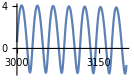

```mathematica
λinit = 3000;       λfin =3200;
Plot[     (*(L.S1)/(Norm[L]Norm[S1])*)  R[[1]] /.sol,{λ, λinit , λfin},PlotRange->All, ImageSize->Small ]
```

```mathematica
Speak["Job done"];
Quit[];
```